```mathematica
Reduce[bhh x(nh-x)+bhl (nh-x)u-gamma x==0 &&blh x(nl-u)+bll u(nl-u)-gamma u==0,{x,u},Reals]
```

Solve::bdomv: Warning: x∈Interval[{0,∞}] is not a valid domain specification. Assuming it is a variable to eliminate.

Solve::ivar: x∈Interval[{0,∞}] is not a valid variable.

Solve[bhl u (nh-x)-gamma x+bhh (nh-x) x==0&&-gamma u+bll (nl-u) u+blh (nl-u) x==0,{x,u},x∈Interval[{0,∞}]]

```mathematica
?Solve
```

Solve[expr,vars] attempts to solve the system expr of equations or inequalities for the variables vars. 
Solve[expr,vars,dom] solves over the domain dom. Common choices of dom are Reals, Integers, and Complexes.

```mathematica
Solve[(2-(a/1000)-x)(0.8-((3600-a)/1000)-x)-0.0016==0,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.001 (-400.-1. √(5.7616×10^6-4800. a+a^2))},{x→0.001 (-400.+√(5.7616×10^6-4800. a+a^2))}}

```mathematica
Reduce[(-400- √(5.7616*10*^6-4800 a+a^2))<0,a>0]
```

Reduce::ivar: a>0 is not a valid variable.

Reduce[-400-√(5.7616×10^7-4800 a+a^2)<0,a>0]

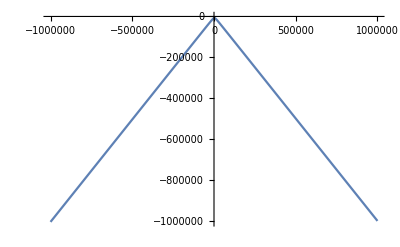

```mathematica
Plot[-400- √(5.7616*10*^6-4800 a+a^2),{a,-10^6,10^6}]
```

```mathematica
Solve[(-400+Sqrt[5.7616*10*^6-4800 a+a^2])<0,a]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{}

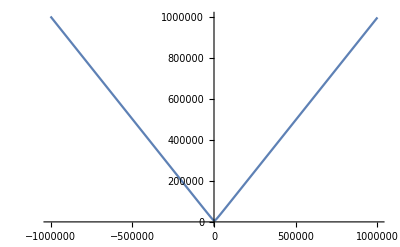

```mathematica
Plot[(-400+Sqrt[5.7616*10*^6-4800 a+a^2]),{a,-10^6,10^6}]
```

```mathematica
m[a_]={{2-0.001 a,0.02},{0.08,0.8-0.001 (3600-a)}}
```

Set::write: Tag List in {{2-0.001 a,0.02},{0.08,0.8-0.001 (3600-a)}}[a_] is Protected.

{{2-0.001 a,0.02},{0.08,0.8-0.001 (3600-a)}}

```mathematica
m=MatrixForm[m]
```

(2-0.001 a | 0.02
0.08 | 0.8-0.001 (3600-a))

```mathematica
m
```

(2-0.001 a | 0.02
0.08 | 0.8-0.001 (3600-a))

```mathematica
Evaluate[Eigenvalues[m]]
```

Eigenvalues[(2-0.001 a | 0.02
0.08 | 0.8-0.001 (3600-a))]

```mathematica
M[a_]= m
```

(2-0.001 a | 0.02
0.08 | 0.8-0.001 (3600-a))

```mathematica
M[1]
```

(1.999 | 0.02
0.08 | -2.799)

```mathematica
Eigenvalues[M[a]]
```

Eigenvalues[(2-0.001 a | 0.02
0.08 | 0.8-0.001 (3600-a))]

```mathematica
m
```

{{2-0.001 a,0.02},{0.08,0.8-0.001 (3600-a)}}

```mathematica
G[a_]={{2-0.001 a-1,0.02},{0.08,0.8-0.001 (3600-a)-1}}
```

{{1-0.001 a,0.02},{0.08,-0.2-0.001 (3600-a)}}

```mathematica
MatrixForm[G[a]]
```

(1-0.001 a | 0.02
0.08 | -0.2-0.001 (3600-a))

```mathematica
Eigenvalues[G[a]]
```

{5.×10^-7 (-2.8×10^6-√(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)),5.×10^-7 (-2.8×10^6+√(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2))}

```mathematica
Eigenvectors[G[a]]
```

{{-1. (-30.+0.0125 a+6.25×10^-6 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)),1.},{-1. (-30.+0.0125 a-6.25×10^-6 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)),1.}}

```mathematica
G[a]
```

{{1-0.001 a,0.02},{0.08,-0.2-0.001 (3600-a)}}

```mathematica
H[a]=G[a]-{{5.*^-7 (-2.8*^6+√(2.30464*^13-1.9200000000000004*^10 a+4.*^6 a^2)),0},{0,5.*^-7 (-2.8*^6+√(2.30464*^13-1.9200000000000004*^10 a+4.*^6 a^2))}}
```

{{1-0.001 a-5.×10^-7 (-2.8×10^6+√(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)),0.02},{0.08,-0.2-0.001 (3600-a)-5.×10^-7 (-2.8×10^6+√(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2))}}

```mathematica
1.9200000000000004*^10
```

1.92×10^10

```mathematica
G[a]
```

{{1-0.001 a,0.02},{0.08,-0.2-0.001 (3600-a)}}

```mathematica
Eigensystem[G[a]]
```

{{-1.4-5.×10^-7 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2),-1.4+5.×10^-7 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)},{{-1. (-30.+0.0125 a+6.25×10^-6 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)),1.},{-1. (-30.+0.0125 a-6.25×10^-6 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)),1.}}}

```mathematica
v1[a_]=-1. (-30.+0.0125 a-6.25*^-6 √(2.30464*^13-1.92*^10 a+4.*^6 a^2));
v2=1;
gammah[a_]=0.001 a+1;
gammal[a_]=0.001(3600-a)+1;
f[a_]=(v1[a]/(v1[a]+v2))(1/gammah[a])+(v2/(v1[a]+v2))(1/gammal[a]);
```

```mathematica
FindMinimum[f[a],a]
```

{0.329554,{a→2180.64}}

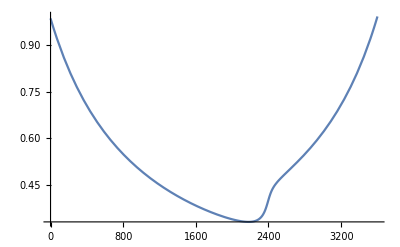

```mathematica
Plot[f[a],{a,0,3600}]
```

```mathematica
J[a_]={{2-0.001 a-1,0.02},{0.08,0.8-0.001(3600-a)-1}}
```

{{1-0.001 a,0.02},{0.08,-0.2-0.001 (3600-a)}}

```mathematica
J[a]//MatrixForm
```

(1-0.001 a | 0.02
0.08 | -0.2-0.001 (3600-a))

```mathematica
l1[a_]=Part[Eigenvalues[J[a]],1]
```

5.×10^-7 (-2.8×10^6-√(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2))

```mathematica
l2[a_]=Part[Eigenvalues[J[a]],2]
```

5.×10^-7 (-2.8×10^6+√(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2))

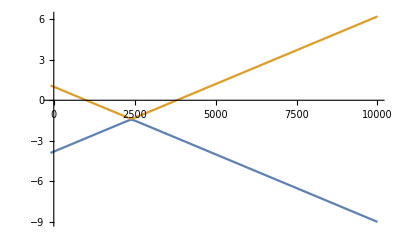

```mathematica
Plot[{l1[a],l2[a]},{a,-100,10000}]
```

```mathematica
Eigensystem[J[a]]
```

{{-1.4-5.×10^-7 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2),-1.4+5.×10^-7 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)},{{-1. (-30.+0.0125 a+6.25×10^-6 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)),1.},{-1. (-30.+0.0125 a-6.25×10^-6 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)),1.}}}

```mathematica
l1[a]
```

5.×10^-7 (-2.8×10^6-√(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2))

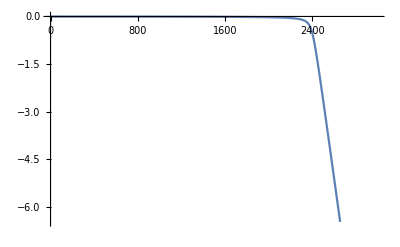

```mathematica
Plot[v1[a],{a,0,3000}]
```

```mathematica
Solve[l2[a]==0]
```

{{a→1000.57},{a→3799.43}}

```mathematica
v1[a_]=Part[Part[Part[Eigensystem[J[a]],2],1],1];
v2=Part[Part[Part[Eigensystem[J[a]],2],1],2];
```

```mathematica
gammah[a_]=0.001a+1;
gammal[a_]=0.001 (3600-a)+1;
```

```mathematica
f[a_]=(2.08/gammah[a])*(v1[a]/(v1[a]+v2))+(0.82/gammal[a])*(v2[a]/(v1[a]+v2))
```

-((2.08 (-30.+0.0125 a+6.25×10^-6 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)))/((1+0.001 a) (1.-1. (-30.+0.0125 a+6.25×10^-6 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)))))+(0.82 1.[a])/((1+0.001 (3600-a)) (1.-1. (-30.+0.0125 a+6.25×10^-6 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2))))

```mathematica
f[a]
```

-((2.08 (-30.+0.0125 a+6.25×10^-6 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)))/((1+0.001 a) (1.-1. (-30.+0.0125 a+6.25×10^-6 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2)))))+(0.82 1.[a])/((1+0.001 (3600-a)) (1.-1. (-30.+0.0125 a+6.25×10^-6 √(2.30464×10^13-1.92×10^10 a+4.×10^6 a^2))))

```mathematica
Plot[f[x],{x,5,100}]
```

-Graphics-

```mathematica
J[ah_,al_]={{2(1-ah)-1,0.2(1-ah)},{0.8(1-al),1.6(1-al)-1}}
```

{{-1+2 (1-ah),0.2 (1-ah)},{0.8 (1-al),-1+1.6 (1-al)}}

```mathematica
Eigenvalues[J[x,y]][[1]]
```

0.5 (1.6-2. x-1.6 y-√(0.8-2.24 x+4. x^2+0.64 y-5.76 x y+2.56 y^2))

```mathematica
l1[x_,y_]=Eigenvalues[J[x,y]][[1]];
l2[x_,y_]=Eigenvalues[J[x,y]][[2]];
```

```mathematica
Plot3D[{l2[x,y]},{x,0,1},{y,0,1}]
```

-Graphics3D-

-Graphics3D-

```mathematica
l1[x,y]
```

0.5 (1.6-2. x-1.6 y-√(0.8-2.24 x+4. x^2+0.64 y-5.76 x y+2.56 y^2))

```mathematica
l2[x,y]
```

0.5 (1.6-2. x-1.6 y+√(0.8-2.24 x+4. x^2+0.64 y-5.76 x y+2.56 y^2))

```mathematica
Solve[l2[x,y]<0,{x,y}]
```

{{}}

```mathematica
Plo
```

```mathematica
m={{-0.55,0.45,0.3},{0.15,-0.85,0.1},{1.05,1.05,-0.3}}
```

{{-0.55,0.45,0.3},{0.15,-0.85,0.1},{1.05,1.05,-0.3}}

```mathematica
m//MatrixForm
```

(-0.55 | 0.45 | 0.3
0.15 | -0.85 | 0.1
1.05 | 1.05 | -0.3)

```mathematica
Eigensystem[m]
```

{{-1.,-1.,0.3},{{-0.625355,0.110357,0.772497},{-0.12828,-0.458113,0.879589},{0.390567,0.130189,0.911322}}}

```mathematica
0.3905667329424716+0.13018891098082386+0.9113223768657671
```

1.43208

```mathematica
{0.3905667329424716,0.13018891098082386,0.9113223768657671}/1.4320780207890627
```

{0.272727,0.0909091,0.636364}

```mathematica
n1=0.2;n2=0.1,n3=0.7;f=1.5;
ClearAll[m]
J[a1_,a2_,a3_]={{(1-a1)n1 f^2 -1,(1-a1)f^2 n1,(1-a1) n1 f},{(1-a2)n2 f,(1-a2) n2 f-1,(1-a2)n2},{(1-a3)n3 f,(1-a3)n3 f},(1-a3)n3-1}
```

```mathematica
J[a1,a2,a3]//MatrixForm
```

J[a1,a2,a3]

```mathematica
J[x,y,z]
```

J[x,y,z]

```mathematica
m
```

{{-0.55,0.45,0.3},{0.15,-0.85,0.1},{1.05,1.05,-0.3}}

```mathematica
n1=0.2;n2=0.1,n3=0.7;f=1.5;
Z[a1_,a2_,a3_]={{(1-a1)n1 f^2 -1,(1-a1)f^2 n1,(1-a1) n1 f},{(1-a2)n2 f,(1-a2) n2 f-1,(1-a2)n2},{(1-a3)n3 f,(1-a3)n3 f,(1-a3)n3-1}}
```

```mathematica
ZZz[a1,a2,a3]//MatrixForm
```

ZZz[a1,a2,a3]

```mathematica
ZZ[x,y,z]
```

ZZ[x,y,z]